# Solution for Problem 2 by Graph Theory

## Plots

3D

```mathematica
PolyhedronData["TruncatedIcosahedron","Edges"];
Graph3D[UndirectedEdge@@@%]
```

-Graphics3D-

2D

```mathematica
GraphData["TruncatedIcosahedralGraph",{"EdgeCount","FaceCount","VertexCount"}]
```

{90,32,60}

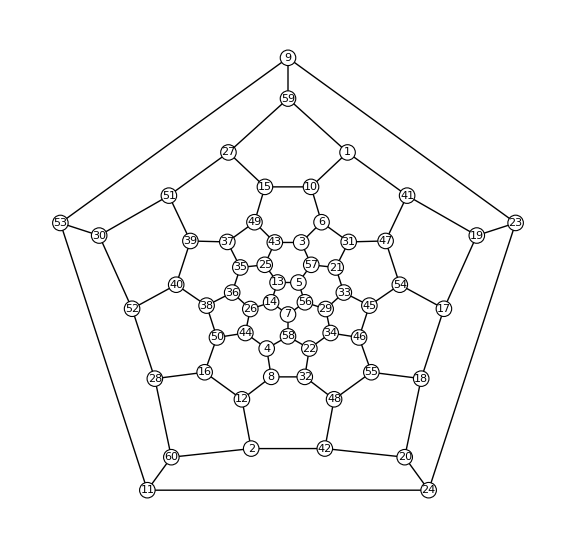

```mathematica
GraphPlot[GraphData["TruncatedIcosahedralGraph"],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.2],Black,Text[#2,#1]}&),PlotStyle->{Black},ImageSize->Large]
```

## Graph Theory

Corresponding to a Max-Cut Problem in Graph Theory

-Graphics-

Max-Cut of Planar Graph Can be Solved in Polynomial Time

The problem of finding a maximum cut of an arbitrary graph is one of a list of 21 combinatorial problems (Karp-Cook list). It is unknown whether or not there exist algorithms operating in polynomial bounded time for any of these problems. It has been shown that existence for one implies existence for all. In this paper we deal with a special case of the maximum cut problem. By requiring the graph to be planar, it is shown the problem can be translated into a maximum weighted matching problem for which there exists a polynomial bounded algorithm.
(FINDING A MAXIMUM CUT OF A PLANAR GRAPHIN POLYNOMIAL TIME*F. HADLOCK,SIAM J. CoMPtrr. Vol. 4, No. 3, September 1975)

## Algorithm

Transformed to Dual

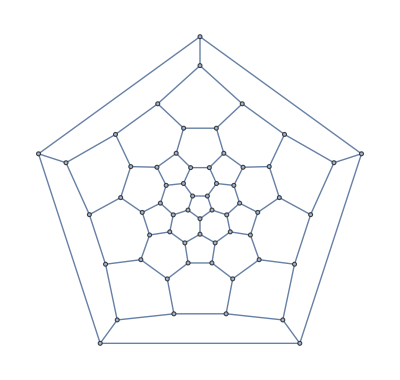

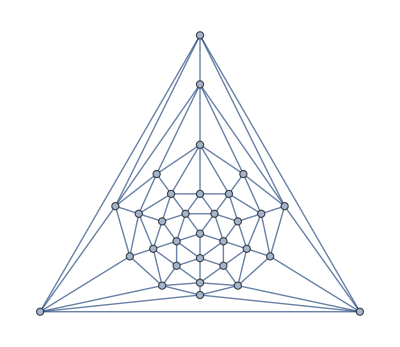

```mathematica
g0=GraphData["TruncatedIcosahedralGraph"]
g1=GraphData["TruncatedIcosahedralGraph","DualGraph"]
```

Ground Energy

```mathematica
VertexDegree[g1]
r=Count[%,_?OddQ]
-90+2r
```

{5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,6,6,6,6,5,5,5,5,6}

12

-66

Degeneracy

Merging those pentagon into a 12 point, A minimum odd-circuit cover may be found by determining a minimum odd pairing of the geometric dual.

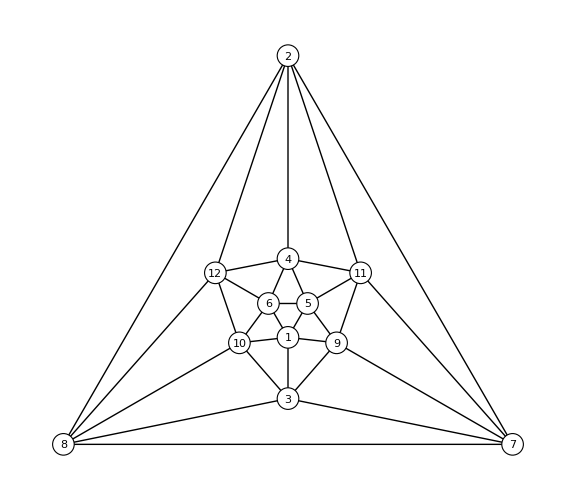

```mathematica
GraphPlot[GraphData["IcosahedralGraph"],VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.15],Black,Text[#2,#1]}&),PlotStyle->{Black},ImageSize->Large]
```

Solve out all parings in python, see  “pair_count”, the result is 125. Then considering the trivial symmetries of the system, we obtain the degeneracy

```mathematica
2*125*2^6
```

16000